In this notebook we check the Ising solution on 1D.

```mathematica
energies3 = Table[{g,J}={1,j};
z = PauliMatrix[3];
x=PauliMatrix[1];
id = IdentityMatrix[2];h = -(g)*(KroneckerProduct[KroneckerProduct[KroneckerProduct[z, id], id],id] +
KroneckerProduct[KroneckerProduct[KroneckerProduct[id, z], id],id]+KroneckerProduct[KroneckerProduct[KroneckerProduct[id, id], z],id]+KroneckerProduct[KroneckerProduct[KroneckerProduct[id, id], id],z])-
(J)*(KroneckerProduct[KroneckerProduct[KroneckerProduct[x, x], id],id]+KroneckerProduct[KroneckerProduct[KroneckerProduct[id, x], x],id]+KroneckerProduct[KroneckerProduct[KroneckerProduct[id, id], x],x]+KroneckerProduct[KroneckerProduct[KroneckerProduct[x, id], id],x]);
{j,Sort[Eigenvalues[h]][[1]]}
,{j,.01,4.1,.4}];
```

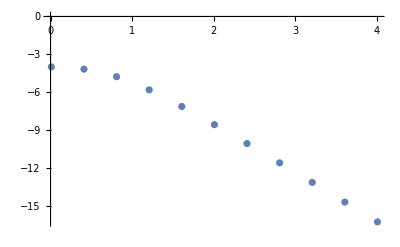

```mathematica
ListPlot[energies3]
```

Now the analytic solution some L

```mathematica
Divisible[8,2]
```

True

```mathematica
L=3;
Kp0 = Table[
2*n*Pi/L,{n,(-L+1)/2,(L-1)/2}];
Kp1 =Union[ Table[(((2*n)-1)*Pi)/L,{n,1,(L-1)/2}],Table[(((2*n)-1)*Pi)/L,{n,-(L-1)/2,0}]];
totalK={};
Do[j=Kp0[[k]];
If[j==0 || j==Pi||j==-Pi,None,AppendTo[totalK,j]],{k,1,Length[Kp0]}];
Do[j=Kp1[[k]];
If[j==0 || j==Pi||j==-Pi,None,AppendTo[totalK,j]],{k,1,Length[Kp1]}];
totalK
```

{-(2 π)/3,(2 π)/3,-π/3,π/3}

```mathematica
Do[j=Kp0[[k]];
If[j==0 || j==Pi||j==-Pi,None,AppendTo[totalK,j]],{k,1,Length[Kp0]}];
Do[j=Kp1[[k]];
If[j==0 || j==Pi||j==-Pi,None,AppendTo[totalK,j]],{k,1,Length[Kp1]}];
```

```mathematica
e[k_,J_,h_]:=2*J*Sqrt[(Cos[k]-h/J)^2+(Sin[k])^2];
eg[J_,h_]:=(
gg=-2*J;
Do[it=totalK[[r]];
If[0<it<Pi,gg=gg-e[it,J,h]],{r,1,Length[totalK]}];gg)
```

```mathematica
enAn=Table[{j,eg[j,1]},{j,.01,4.1,.4}];
enAn
```

{{0.01,-4.02015},{0.41,-5.07383},{0.81,-6.60044},{1.21,-8.49332},{1.61,-10.5974},{2.01,-12.8118},{2.41,-15.0866},{2.81,-17.3968},{3.21,-19.7295},{3.61,-22.0772},{4.01,-24.4353}}

```mathematica
energies3
```

{{0.01,-4.0001},{0.41,-4.17816},{0.81,-4.77671},{1.21,-5.82211},{1.61,-7.13885},{2.01,-8.58003},{2.41,-10.0803},{2.81,-11.6122},{3.21,-13.1626},{3.61,-14.7248},{4.01,-16.2951}}

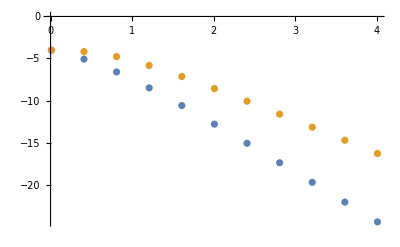

```mathematica
ListPlot[{enAn,energies3}]
```